```mathematica
ⅈ^2
```

-1

```mathematica
Exp[ⅈ π]
```

-1

```mathematica
I^2==f[I π]
```

-1==f[ⅈ π]

```mathematica
ApplySides[-1==f[ⅈ π],InverseFunction[f]]
```

ApplySides::eqin: f^(-1) should be an equation or an inequality.

ApplySides[-1==f[ⅈ π],f^(-1)]

```mathematica
InverseFunction[f][-1]==ⅈ π
```

f^(-1)[-1]==ⅈ π

```mathematica
Dt[f[x]]==Dt[x]f'[x]
```

True

```mathematica
Dt[Dt[f[x]]]
```

Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]

```mathematica
TraditionalForm[Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]]
```

(ⅆx)^2 f''(x)+ⅆ(ⅆx) f'(x)

```mathematica
Dt[Dt[f[x]]]==g'[x]
```

Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]==g'[x]

```mathematica
Dt[x]
```

Dt[x]

```mathematica
Dt[Dt[f[x]]]==Dt[g[x]]
```

Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]==Dt[x] g'[x]

```mathematica
Dt[Dt[x]]==Dt[x]^2
```

Dt[Dt[x]]==Dt[x]^2

```mathematica
Limit[Sum[1/k^2,{k,1,a}],a->∞]
```

π^2/6

```mathematica
√(6Limit[Sum[1/k^2,{k,1,a}],a->∞])
```

π

```mathematica
Integrate[√(x^2-1),x]
```

1/2 x √(-1+x^2)-1/2 Log[x+√(-1+x^2)]

```mathematica
CoefficientList[1,2,3,4]
```

CoefficientList::nonopt: Options expected (instead of 4) beyond position 3 in CoefficientList[1,2,3,4]. An option must be a rule or a list of rules.

CoefficientList[1,2,3,4]

```mathematica
CoefficientList[{1,2,3,4}]
```

CoefficientList::argtu: CoefficientList called with 1 argument; 2 or 3 arguments are expected.

CoefficientList[{1,2,3,4}]

```mathematica
Coefficient[4]
```

Coefficient::argtu: Coefficient called with 1 argument; 2 or 3 arguments are expected.

Coefficient[4]

```mathematica
x^4-4 x^3+2 x^2+4x+4
```

4+4 x+2 x^2-4 x^3+x^4

```mathematica
FindRoot[4+4 x+2 x^2-4 x^3+x^4]
```

FindRoot::argmu: FindRoot called with 1 argument; 2 or more arguments are expected.

FindRoot[4+4 x+2 x^2-4 x^3+x^4]

```mathematica
FindRoot[4+4 x+2 x^2-4 x^3+x^4,{x}]
```

FindRoot::srect: Value x in search specification {x} is not a number or array of numbers.

FindRoot[4+4 x+2 x^2-4 x^3+x^4,{x}]

```mathematica
So
```

```mathematica
Solve[4+4 x+2 x^2-4 x^3+x^4,{x}]
```

Solve::naqs: 4+4 x+2 x^2-4 x^3+x^4 is not a quantified system of equations and inequalities.

Solve[4+4 x+2 x^2-4 x^3+x^4,{x}]

```mathematica
Solve[4+4 x+2 x^2-4 x^3+x^4,x]
```

Solve::naqs: 4+4 x+2 x^2-4 x^3+x^4 is not a quantified system of equations and inequalities.

Solve[4+4 x+2 x^2-4 x^3+x^4,x]

```mathematica
Solve[4+4 x+2 x^2-4 x^3+x^4==0,x]
```

{{x→1-√(2-ⅈ √3)},{x→1+√(2-ⅈ √3)},{x→1-√(2+ⅈ √3)},{x→1+√(2+ⅈ √3)}}

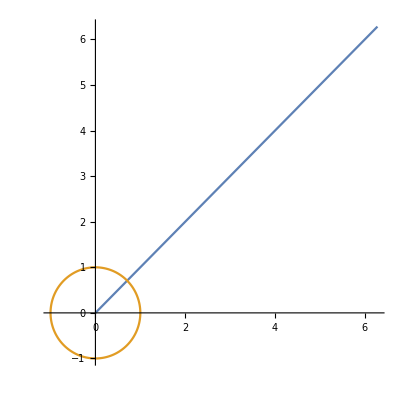

```mathematica
ParametricPlot[{
{t,t},
{Cos[t],Sin[t]}
},{t,0,2π}]
```

```mathematica
ParametricPlot[{
{t,t},
{Cos[t],Sin[t]}
},{t,0,2π}]
```

```mathematica
(1-a)p +a q/.{p->{t,t},q-> {Cos[t],Sin[t]}}
```

{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}

```mathematica
Manipulate[
ParametricPlot[{
{t,t},
{Cos[t],Sin[t]},
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}
},{t,0,2π}]
,{a,0,1}]
```

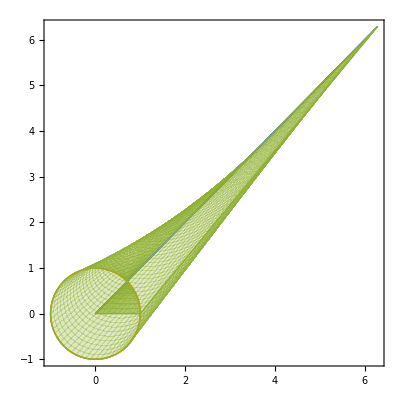

```mathematica
ParametricPlot[{
{t,t},
{Cos[t],Sin[t]},
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}
},{t,0,2π},{a,0,1}]
```

```mathematica
Norm[Integrate[Integrate[{(1-a) t+a Cos[t],(1-a) t+a Sin[t]},{a,0,1}],{t,0,2π}]]
```

√2 π^2

```mathematica
N[√2 π^2]
```

13.9577

```mathematica
Norm[Integrate[Integrate[{(1-a) t+a Cos[t],(1-a) t+a Sin[t]},{t,0,2π}],{a,0,1}]]
```

√2 π^2

```mathematica
{(1-a) t+a Cos[t],(1-a) t+a Sin[t]}/.a->1
```

{Cos[t],Sin[t]}

```mathematica
{Cos[t],Sin[t]}-{t,t}
```

{-t+Cos[t],-t+Sin[t]}

```mathematica
Norm[{-t+Cos[t],-t+Sin[t]}]
```

√(Abs[-t+Cos[t]]^2+Abs[-t+Sin[t]]^2)

```mathematica
√((-t+Cos[t])^2+(-t+Sin[t])^2)
```

√((-t+Cos[t])^2+(-t+Sin[t])^2)

```mathematica
FullSimplify[√((-t+Cos[t])^2+(-t+Sin[t])^2)]
```

√(1+2 t^2-2 t (Cos[t]+Sin[t]))

```mathematica
Integrate[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,0,2π}]
```

$Aborted

```mathematica
NIntegrate[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,0,2π}]
```

28.9736

```mathematica
(1-a)p+a q/.{p->{t,1},q->{t,3}}
```

{(1-a) t+a t,1+2 a}

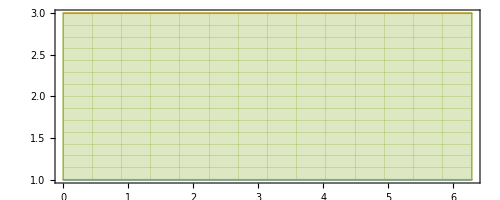

```mathematica
ParametricPlot[{
{t,1},
{t,3},
{(1-a) t+a t,1+2 a}
},{t,0,2π},{a,0,1}]
```

```mathematica
Manipulate[
ParametricPlot[{
{t,1},
{t,3},
{(1-a) t+a t,1+2 a}
},{t,0,2π}],{a,0,1}]
```

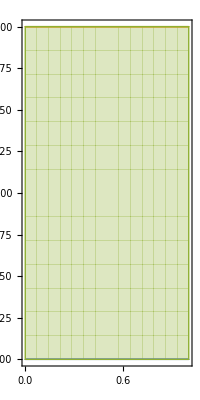

```mathematica
ParametricPlot[{
{t,1},
{t,3},
{(1-a) t+a t,1+2 a}
},{t,0,1},{a,0,1}]
```

```mathematica
Norm[Integrate[Integrate[{(1-a) t+a t,1+2 a},{a,0,1}],{t,0,1}]]
```

(√17)/2

```mathematica
N[(√17)/2]
```

2.06155

```mathematica
Integrate[Integrate[{(1-a) t+a t,1+2 a},{a,0,1}],{t,0,1}]
```

{1/2,2}

```mathematica
Norm[{t,3}-{t,1}]
```

2

```mathematica
{t,3}-{t,1}
```

{0,2}

```mathematica
Integrate[Integrate[Norm[{(1-a) t+a t,1+2 a}],{a,0,1}],{t,0,1}]
```

1/12 (-2 √2+6 √10+27 ArcCsch[3]-2 ArcSinh[1]+ArcSinh[3])

```mathematica
N[1/12 (-2 √2+6 √10+27 ArcCsch[3]-2 ArcSinh[1]+ArcSinh[3])]
```

2.08684

```mathematica
{Cos[t],Sin[t]}-{t,t}
```

{-t+Cos[t],-t+Sin[t]}

```mathematica
Norm[{Cos[t],Sin[t]}-{t,t}]
```

√(Abs[-t+Cos[t]]^2+Abs[-t+Sin[t]]^2)

```mathematica
FullSimplify[√(Abs[-t+Cos[t]]^2+Abs[-t+Sin[t]]^2)]
```

√(Abs[t-Cos[t]]^2+Abs[t-Sin[t]]^2)

```mathematica
√((-t+Cos[t])^2+(-t+Sin[t])^2)
```

√((-t+Cos[t])^2+(-t+Sin[t])^2)

```mathematica
FullSimplify[√((-t+Cos[t])^2+(-t+Sin[t])^2)]
```

√(1+2 t^2-2 t (Cos[t]+Sin[t]))

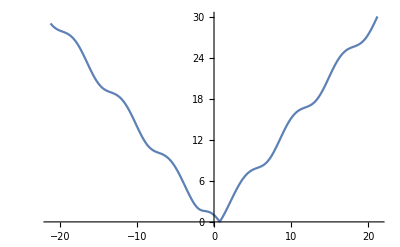

```mathematica
Plot[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,-21.205750411731103,21.205750411731103}]
```

```mathematica
NIntegrate[√(1+2 t^2-2 t (Cos[t]+Sin[t])),{t,0,2π}]
```

28.9736

```mathematica
Norm[D[{-t+Cos[t],-t+Sin[t]},t]]
```

√(Abs[-1+Cos[t]]^2+Abs[-1-Sin[t]]^2)

```mathematica
√((-1+Cos[t])^2+(-1-Sin[t])^2)
```

√((-1+Cos[t])^2+(-1-Sin[t])^2)

```mathematica
ExpandAll[√((-1+Cos[t])^2+(-1-Sin[t])^2)]
```

√(2-2 Cos[t]+Cos[t]^2+2 Sin[t]+Sin[t]^2)

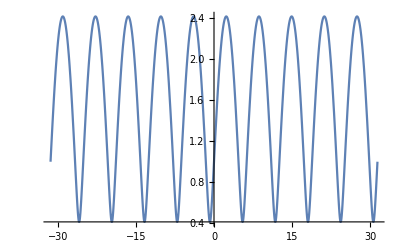

```mathematica
Plot[√(2-2 Cos[t]+Cos[t]^2+2 Sin[t]+Sin[t]^2),{t,-10 π,10 π}]
```

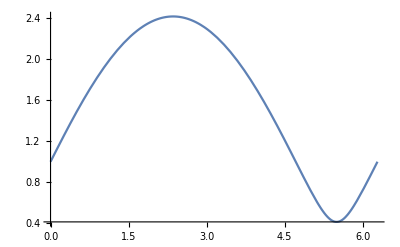

```mathematica
Plot[√(2-2 Cos[t]+Cos[t]^2+2 Sin[t]+Sin[t]^2),{t,0,2π}]
```

```mathematica
Nest[Dt,f[x],2]
```

Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]

```mathematica
Integrate[Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x],x]
```

∫(Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x])ⅆx

```mathematica
Integrate[Dt[f[x]],x]
```

∫Dt[x] f'[x]ⅆx

```mathematica
Integrate[f'[x],x]
```

f[x]

```mathematica
∫(Dt[Dt[x]] f'[x])ⅆx+∫(Dt[x]^2 f''[x])ⅆx
```

```mathematica
g[x]==Dt[Dt[f[x]]]
```

g[x]==Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]

```mathematica
Integrate[Integrate[Dt[Dt[f[x]]],x],x]
```

∫(∫(Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x])ⅆx)ⅆx

```mathematica
Integrate[Integrate[Dt[Dt[f[x]]],x],x]==f[x]
```

∫(∫(Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x])ⅆx)ⅆx==f[x]

```mathematica
TraditionalForm[Integrate[Integrate[Dt[Dt[f[x]]],x],x]==f[x]]
```

∫(∫((ⅆx)^2 f''(x)+ⅆ(ⅆx) f'(x))ⅆx)ⅆx==f(x)

```mathematica
FullSimplify[Dt[Dt[f[x]]],{x,f[x]}∈Reals]
```

Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]

```mathematica
∫_0^1 xⅆx
```

1/2

```mathematica
Integrate[Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x],x]==f'[x]
```

∫(Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x])ⅆx==f'[x]

```mathematica
TraditionalForm[∫(Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x])ⅆx==f'[x]]
```

∫((ⅆx)^2 f''(x)+ⅆ(ⅆx) f'(x))ⅆx==f'(x)

```mathematica
TraditionalForm[∫(Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x])ⅆx==f'[x]Dt[x]]
```

∫((ⅆx)^2 f''(x)+ⅆ(ⅆx) f'(x))ⅆx==ⅆx f'(x)

```mathematica
Integrate[f'[x]Dt[x],x]
```

∫Dt[x] f'[x]ⅆx

```mathematica
Attributes[Dt]
```

{Protected,ReadProtected}

```mathematica
Options[Dt]
```

{Constants→{}}

```mathematica
Dt[α f[x] g[x],Constants->{α}]
```

α Dt[x,Constants→{α}] g[x] f'[x]+α Dt[x,Constants→{α}] f[x] g'[x]

```mathematica
Dt[α f[x] g[x],Constants->α]
```

α Dt[x,Constants→{α}] g[x] f'[x]+α Dt[x,Constants→{α}] f[x] g'[x]

```mathematica
Dt[α f[x] g[x]]
```

Dt[α] f[x] g[x]+α Dt[x] g[x] f'[x]+α Dt[x] f[x] g'[x]

```mathematica
Dt[f[x]g[x]]
```

Dt[x] g[x] f'[x]+Dt[x] f[x] g'[x]

```mathematica
TraditionalForm[Dt[x] g[x] f'[x]+Dt[x] f[x] g'[x]]
```

g(x) ⅆx f'(x)+f(x) ⅆx g'(x)

```mathematica
Integrate[(g[x] f'[x]+f[x] g'[x]),x]
```

f[x] g[x]

```mathematica
TraditionalForm[∫(Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x])ⅆx==f'[x]Dt[x]]
```

∫((ⅆx)^2 f''(x)+ⅆ(ⅆx) f'(x))ⅆx==ⅆx f'(x)

```mathematica
Dt[Dt[f[x]]]
```

Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]

```mathematica
Integrate[Integrate[Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x],x],x]==f[x]
```

∫(∫(Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x])ⅆx)ⅆx==f[x]

```mathematica
Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]
```

Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]

```mathematica
TraditionalForm[Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]]
```

(ⅆx)^2 f''(x)+ⅆ(ⅆx) f'(x)

```mathematica
Dt[Dt[Dt[x]]]
```

Dt[Dt[Dt[x]]]

```mathematica
g[f[x]]==f'[x]
```

g[f[x]]==f'[x]

```mathematica
DSolve[g[f[x]]==f'[x],{f[x]},{x}]
```

{{f[x]→InverseFunction[1/g[K[1]]K[1]1#1&][x+C[1]]}}

```mathematica
Activate[InverseFunction[1/g[K[1]]K[1]1#1&][x+C[1]]]
```

InverseFunction[∫_1^#1 1/g[K[1]]ⅆK[1]&][x+C[1]]

```mathematica
(∫_1^#1 1/g[K[1]] ⅆK[1]&)[x+C[1]]
```

∫_1^(x+C[1]) 1/g[K[1]]ⅆK[1]

```mathematica
(∫_1^#1 1/g[K[1]] ⅆK[1]&)[s+C[1]]
```

∫_1^(s+C[1]) 1/g[K[1]]ⅆK[1]

```mathematica
∫_1^(s+C[1]) 1/g[K[1]] ⅆK[1]/.K[1]->x
```

∫_1^(s+C[1]) 1/g[x]ⅆx

```mathematica
∫_1^s 1/g[x] ⅆx
```

∫_1^s 1/g[x]ⅆx

```mathematica
With[{g=Function[x,x]},∫_1^s 1/g[x] ⅆx]
```

ConditionalExpression[Log[s],Re[s]>0||s∉ℝ]

```mathematica
With[{g=Function[x,x x]},∫_1^s 1/g[x] ⅆx]
```

ConditionalExpression[1-1/s,Re[s]>0||s∉ℝ]

```mathematica
With[{g=Function[x,x x]},FullSimplify[∫_1^s 1/g[x] ⅆx,s∈Reals]]
```

ConditionalExpression[(-1+s)/s,s>0]

```mathematica
With[{g=Function[x,x x]},FullSimplify[∫_1^s 1/g[x] ⅆx,s∈Reals]]
```

```mathematica
PositiveReals
```

```mathematica
With[{g=Function[x,x x]},FullSimplify[∫_1^s 1/g[x] ⅆx,s∈]]
```

(-1+s)/s

```mathematica
With[{g=Function[x,Log[x x]]},FullSimplify[∫_1^s 1/g[x] ⅆx,s∈]]
```

Integrate::idiv: Integral of 1/Log[x^2] does not converge on {1,s}.

∫_1^s 1/Log[x^2]ⅆx

```mathematica
With[{g=Function[x,Log[x]]},FullSimplify[∫_1^s 1/g[x] ⅆx,s∈]]
```

Integrate::idiv: Integral of 1/Log[x] does not converge on {1,s}.

∫_1^s 1/Log[x]ⅆx

```mathematica
With[{g=Function[x,x x + x]},FullSimplify[∫_1^s 1/g[x] ⅆx,s∈]]
```

Log[(2 s)/(1+s)]

```mathematica
With[{f=Identity},Exp[f'[x]/f[x]]]
```

ⅇ^(1/x)

```mathematica
g[Exp[Power[x,-1]]]==x
```

g[ⅇ^(1/x)]==x

```mathematica
Reduce[g[ⅇ^(1/x)]==x]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[g[ⅇ^(1/x)]==x]

```mathematica
DSolve[g[ⅇ^(1/x)]==x,{g[x]},x]
```

{}

```mathematica
InverseFunction[g][g[ⅇ^(1/x)]]==InverseFunction[g][x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

ⅇ^(1/x)==g^(-1)[x]

```mathematica
Dt[Dt[f[x]]]
```

Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]

```mathematica
TraditionalForm[Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]==g[x]]
```

(ⅆx)^2 f''(x)+ⅆ(ⅆx) f'(x)==g(x)

```mathematica
f[x]==f'[x]/Dt[x] Dt[x]
```

f[x]==f'[x]

```mathematica
f[x]==f[x]/Dt[x] Dt[x]
```

True

```mathematica
f'[x]==f[x]/Dt[x]
```

f'[x]==f[x]/Dt[x]

```mathematica
Dt[f[x]]
```

Dt[x] f'[x]

```mathematica
Dt[f[x]]==f[x]
```

Dt[x] f'[x]==f[x]

```mathematica
f''[x]==f'[x]/Dt[x]==(f[x]/Dt[x])/Dt[x]
```

f''[x]==f'[x]/Dt[x]==f[x]/Dt[x]^2

```mathematica
f''[x]==f'[x]/Dt[x]==(f[x]/Dt[x])/Dt[x]
```

```mathematica
a/(b/b)
```

a

```mathematica
(a/b)/b
```

a/b^2

```mathematica
f''[x]==f'[x]/Dt[x]==(f[x]/Dt[x])/Dt[x]==f[x]/Dt[x]^2
```

f''[x]==f'[x]/Dt[x]==f[x]/Dt[x]^2==f[x]/Dt[x]^2

```mathematica
(f^(n))[x]==f[x]/Dt[x]^n
```

f^n[x]==Dt[x]^-n f[x]

```mathematica
23+5
```

28

```mathematica
Nest[1+#&,1,2]
```

3

```mathematica
Nest[1+#&,1,n]
```

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[1+#1&,1,n].

Nest[1+#1&,1,n]

```mathematica
Dt[Dt[f[x]]]
```

Dt[Dt[x]] f'[x]+Dt[x]^2 f''[x]

```mathematica
Dt[Dt[x]] f'[x]==0
```

Dt[Dt[x]] f'[x]==0

```mathematica
TraditionalForm[Integrate[Dt[Dt[x]] f'[x],x]==0]
```

∫ⅆ(ⅆx) f'(x)ⅆx==0

```mathematica
TraditionalForm[Integrate[Dt[Dt[x]] f'[x]/Dt[x],x]==0]
```

∫(ⅆ(ⅆx) f'(x))/ⅆx ⅆx==0

```mathematica
Dt[Dt[x]] f'[x]
```

Dt[Dt[x]] f'[x]

```mathematica
x==x'/Dt[x]
```